SimulationTools > Binary systems

# Binary Systems

Simulations of binary systems, for example binary black hole or binary neutron star simulations in numerical relativity, are supported.  It is assumed that there is only one binary in a simulation, and functions are provided to access the coordinate properties of the members of the binary, as well as their relative orbit.  The members of the binary are identified by integers 1 and 2.  In general, if no member index is given, the result refers to the relative orbit of the binary.

The binaries functions work with simulation data from the PunctureTracker, MinTracker, ShiftTracker and AHFinderDirect codes, as well those in Numerical Relativity Data Format (NRDF).

## Working with binary systems

```mathematica
<<SimulationTools`
```

```mathematica
$SimulationPath={$SimulationToolsTestSimulationDirectory}
```

{/Users/ian/Library/Mathematica/Applications/SimulationTools/Data/Simulations}

```mathematica
run="bbh";
```

ReadBinarySeparation | ReadBinaryPhase
ReadBinaryCoordinates | ToListOfPoints

Functions for reading black hole information.

### Orbital separation

The function ReadBinarySeparation gives the distance between the two members of the binary as a function of time.

```mathematica
r=ReadBinarySeparation[run]
```

DataTable[<601>,{{0,300}}]

```mathematica
Take[ToList[r],10]
```

{{0,6},{0.5,5.99902},{1,5.99523},{1.5,5.99151},{2,5.98945},{2.5,5.98897},{3,5.99011},{3.5,5.99308},{4,5.9976},{4.5,6.00337}}

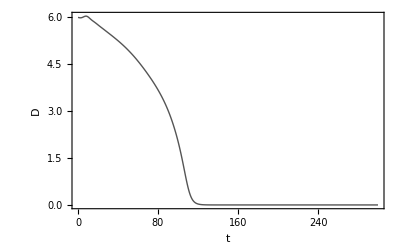

```mathematica
PresentationListLinePlot[r,FrameLabel->{"t","D"}]
```

### Orbital phase

ReadBinaryPhase gives the orbital phase, or azimuthal angle (in radians) projected into the xy plane, of the relative orbit vector (i.e. the vector joining the two members of the binary).

```mathematica
phi=ReadBinaryPhase[run]
```

DataTable[<601>,{{0,300}}]

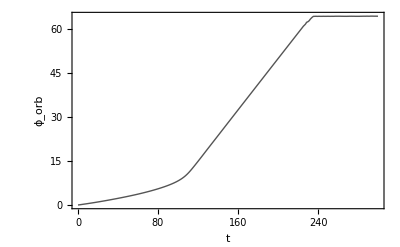

```mathematica
PresentationListLinePlot[phi,FrameLabel->{"t","ϕ_orb"}]
```

### Trajectories

The function ReadBinaryCoordinates gives a list of coordinates x, y and z.  Each is a DataTable containing a coordinate position as a function of time.

```mathematica
path1={x1,y1,z1}=ReadBinaryCoordinates[run,1]
```

{DataTable[<601>,{{0,300}}],DataTable[<601>,{{0,300}}],DataTable[<601>,{{0,300}}]}

```mathematica
path2={x2,y2,z2}=ReadBinaryCoordinates[run,2]
```

{DataTable[<601>,{{0,300}}],DataTable[<601>,{{0,300}}],DataTable[<601>,{{0,300}}]}

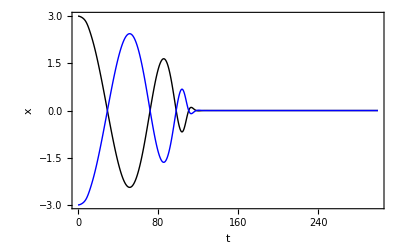

```mathematica
PresentationListLinePlot[{x1,x2},PlotRange->All,FrameLabel->{"t","x"}]
```

If no binary index is given, then the coordinates are of the relative orbit.

The function ToListOfPoints can be used to convert a list of coordinate DataTables into a list of points suitable for plotting:

```mathematica
Take[ToListOfPoints[path1],10]
```

{{3,0,0},{2.99949,0.0115049,-1.27624×10^-20},{2.99698,0.0615985,4.12171×10^-20},{2.99287,0.131566,7.26335×10^-20},{2.98756,0.206967,1.00965×10^-19},{2.98119,0.281867,3.94664×10^-20},{2.9738,0.356226,3.67029×10^-20},{2.96542,0.430718,4.97394×10^-20},{2.95593,0.505288,1.7777×10^-19},{2.94517,0.579732,2.54703×10^-19}}

```mathematica
Graphics3D[{Darker@Green,Line[ToListOfPoints[path1]],Blue,Line[ToListOfPoints[path2]]},PlotRange->{All,All,{-1,1}},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

### Interpolated coordinates

Sometime you may not want to consider the discrete output of the simulation.  You can use Interpolation on DataTables to create a function containing the coordinates:

```mathematica
pos=Module[{xFn=Interpolation[x1],yFn=Interpolation[y1],zFn=Interpolation[z1]},
Function[t,{xFn[t],yFn[t],zFn[t]}]]
```

Function[t$,{xFn$955463[t$],yFn$955463[t$],zFn$955463[t$]}]

```mathematica
pos[3.5]
```

{2.96542,0.430718,4.97394×10^-20}

## Implementation notes

SimulationTools obtains binary system information (in order of preference) from any of the following sources:

PunctureTracker Cactus output

AHFinderDirect Cactus output

MinTracker Cactus output

ShiftTracker Cactus output

Numerical Relativity Data Format (NRDF) output files [not yet implemented]

In all cases, the binary members are numbered in the same sequence as the output data, and it is assumed that the first two tracked objects correspond to the binary.  For PunctureTracker, MinTracker and ShiftTracker, trackers 0 and 1 correspond to binary members 1 and 2.  For AHFinderDirect and NRDF, the mapping between tracker index and binary member is one to one.

RELATED TUTORIALS

DataTable

NumericalRelativity

BlackHoles